## DelaunayMean-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 05:00:45
using xCellerator 0.90 and XSSA 1204002

Generate 100 random points and their Delaunay Triangulation

```mathematica
r:=RandomReal[{0, 10}]; 
v=Table[{r,r}, {100}];
```

```mathematica
de=DelaunayEdges[v];
```

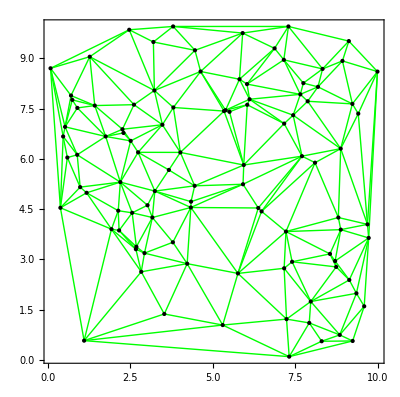

```mathematica
Show[Graphics[{Green,Line/@de}], Graphics[Point/@v] , Frame-> True]
```

```mathematica
DelaunayMean[v]
```

1.20878